## Лабораторная работа №6

```mathematica
n=3;
```

```mathematica
m=2;
```

```mathematica
μ=((n+m)*(n+m-1))/2
```

10

```mathematica
SS=Table[Subscript[S, i]=i,{i,0,m}]
```

{0,1,2}

```mathematica
t={};
```

```mathematica
i=1;
Do[If[j+k+l<m+1,{t=Join[t,{{Subscript[S, j],Subscript[S, k],Subscript[S, l]}}],Subscript[ϕ, i][x_,y_,z_]=x^Subscript[S, j] y^Subscript[S, k] z^Subscript[S, l],i=i+1}],{j,0,m},{k,0,m},{l,0,m}]
```

```mathematica
t
```

{{0,0,0},{0,0,1},{0,0,2},{0,1,0},{0,1,1},{0,2,0},{1,0,0},{1,0,1},{1,1,0},{2,0,0}}

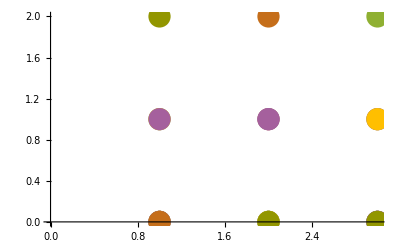

```mathematica
ListPlot[t,PlotStyle->PointSize[0.04]]
```

```mathematica
Table[Subscript[ϕ, i][x,y,z],{i,1,μ}]
```

{1,z,z^2,y,y z,y^2,x,x z,x y,x^2}

```mathematica
V=Table[Subscript[ϕ, j][t[[i,1]],t[[i,2]],t[[i,3]]],{i,1,μ},{j,1,μ}];
```

```mathematica
MatrixForm[V]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 2 | 0 | 4 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 4)

```mathematica
Det[V]≠0
```

True

```mathematica
F[x_,y_,z_]=yz^5+x*Sin[y]^2;
```

```mathematica
Equation=Table[∑_(i=1)^μ Subscript[b, i]*Subscript[ϕ, i][t[[j,1]],t[[j,2]],t[[j,3]]]==F[t[[j,1]],t[[j,2]],t[[j,3]]],{j,1,μ}]
```

{b_1==yz^5,b_1+b_2+b_3==yz^5,b_1+2 b_2+4 b_3==yz^5,b_1+b_4+b_6==yz^5,b_1+b_2+b_3+b_4+b_5+b_6==yz^5,b_1+2 b_4+4 b_6==yz^5,b_1+b_7+b_10==yz^5,b_1+b_2+b_3+b_7+b_8+b_10==yz^5,b_1+b_4+b_6+b_7+b_9+b_10==yz^5+Sin[1]^2,b_1+2 b_7+4 b_10==yz^5}

```mathematica
koef=Solve[Equation,{}]//Flatten
```

{b_1→yz^5,b_2→0,b_3→0,b_4→0,b_5→0,b_6→0,b_7→0,b_8→0,b_9→Sin[1]^2,b_10→0}

```mathematica
P[x_,y_,z_]=∑_(i=1)^μ Subscript[b, i] Subscript[ϕ, i][x,y,z]//.koef
```

yz^5+x y Sin[1]^2

```mathematica
Table[∑_(i=1)^μ Subscript[b, i] Subscript[ϕ, i][t[[j,1]],t[[j,2]],t[[j,3]]]==F[t[[j,1]],t[[j,2]],t[[j,3]]],{j,1,μ}]//.koef
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
Equation:=Table[∑_(i=1)^μ Subscript[b, i]*Subscript[ϕ, i][t[[j,1]],t[[j,2]],t[[j,3]]]==F[t[[j,1]],t[[j,2]],t[[j,3]]],{j,1,μ}];
koef:=Solve[Equation,{}]//Flatten
P[x_,y_,z_]:=∑_(i=1)^μ Subscript[b, i] Subscript[ϕ, i][x,y,z]//.koef
```

```mathematica
Table[{F[x_,y_,z_]=Subscript[ϕ, i][x,y,z],P[x,y,z]==Subscript[ϕ, i][x,y,z]},{i,1,μ}]//.koef
```

{{1,True},{z,True},{z^2,True},{y,True},{y z,True},{y^2,True},{x,True},{x z,True},{x y,True},{x^2,True}}

```mathematica
Value1={x->t[[m-1,1]],y->t[[m-1,2]],z->t[[m-1,3]]};
```

```mathematica
DP1=D[P[x,y,z],{x,1}]//.Value1//N
```

0.

```mathematica
DF1=D[F[x,y,z],{x,1}]//.Value1//N
```

0.

```mathematica
Value2={x->t[[m,1]],y->t[[m,2]],z->t[[m,3]]};
DP2=D[P[x,y,z],{x,m-2},{y,1},{z,1}]//.Value2//N
```

0.

```mathematica
DF2=D[F[x,y,z],{x,m-2},{y,1},{z,1}]//.Value2//N
```

0.

```mathematica
Value3={x->t[[μ,1]],y->t[[μ,2]],z->t[[μ,3]]};
DP3=D[P[x,y,z],{x,μ-1},{y,1}]//.Value3//N
```

0.

```mathematica
DF3=D[F[x,y,z],{x,μ-1},{y,1}]//.Value3//N
```

0.

```mathematica
DD1=∑_(k=1)^μ Subscript[A, k] F[t[[k,1]],t[[k,2]],t[[k,3]]];
```

```mathematica
eqv1=Table[(D[Subscript[ϕ, i][x,y,z],{x,1}]//.Value1)==∑_(k=1)^μ Subscript[A, k] Subscript[ϕ, i][t[[k,1]],t[[k,2]],t[[k,3]]],{i,1,μ}]
```

{0==A_1+A_2+A_3+A_4+A_5+A_6+A_7+A_8+A_9+A_10,0==A_2+2 A_3+A_5+A_8,0==A_2+4 A_3+A_5+A_8,0==A_4+A_5+2 A_6+A_9,0==A_5,0==A_4+A_5+4 A_6+A_9,1==A_7+A_8+A_9+2 A_10,0==A_8,0==A_9,0==A_7+A_8+A_9+4 A_10}

```mathematica
koef=Solve[eqv1,{}]//Flatten
```

{A_1→-3/2,A_2→0,A_3→0,A_4→0,A_5→0,A_6→0,A_7→2,A_8→0,A_9→0,A_10→-1/2}

```mathematica
DD1=DD1/.koef//N
```

0.

```mathematica
DD2=∑_(k=1)^μ Subscript[A, k] F[t[[k,1]],t[[k,2]],t[[k,3]]];
```

```mathematica
eqv2=Table[(D[Subscript[ϕ, i][x,y,z],{x,m-2},{y,1},{z,1}]//.Value2)==∑_(k=1)^μ Subscript[A, k] Subscript[ϕ, i][t[[k,1]],t[[k,2]],t[[k,3]]],{i,1,μ}]
```

{0==A_1+A_2+A_3+A_4+A_5+A_6+A_7+A_8+A_9+A_10,0==A_2+2 A_3+A_5+A_8,0==A_2+4 A_3+A_5+A_8,0==A_4+A_5+2 A_6+A_9,1==A_5,0==A_4+A_5+4 A_6+A_9,0==A_7+A_8+A_9+2 A_10,0==A_8,0==A_9,0==A_7+A_8+A_9+4 A_10}

```mathematica
koef=Solve[eqv2,{}]//Flatten
```

{A_1→1,A_2→-1,A_3→0,A_4→-1,A_5→1,A_6→0,A_7→0,A_8→0,A_9→0,A_10→0}

```mathematica
DD2=DD2/.koef//N
```

0.

```mathematica
DD3=∑_(k=1)^μ Subscript[A, k] F[t[[k,1]],t[[k,2]],t[[k,3]]];
```

```mathematica
eqv3=Table[(D[Subscript[ϕ, i][x,y,z],{x,μ-1},{y,1}]//.Value3)==∑_(k=1)^μ Subscript[A, k] Subscript[ϕ, i][t[[k,1]],t[[k,2]],t[[k,3]]],{i,1,μ}]
```

{0==A_1+A_2+A_3+A_4+A_5+A_6+A_7+A_8+A_9+A_10,0==A_2+2 A_3+A_5+A_8,0==A_2+4 A_3+A_5+A_8,0==A_4+A_5+2 A_6+A_9,0==A_5,0==A_4+A_5+4 A_6+A_9,0==A_7+A_8+A_9+2 A_10,0==A_8,0==A_9,0==A_7+A_8+A_9+4 A_10}

```mathematica
koef=Solve[eqv3,{}]//Flatten
```

{A_1→0,A_2→0,A_3→0,A_4→0,A_5→0,A_6→0,A_7→0,A_8→0,A_9→0,A_10→0}

```mathematica
DD3=DD3/.koef//N
```

0.

```mathematica
DP1==DD1
```

True

```mathematica
DP2==DD2
```

True

```mathematica
DP3==DD3
```

True